```mathematica
(* ::Package:: *)

(* ================================================================
   CELL 1 / 5 - SETUP
   Algebra, kernels, and four structural cores.
   Produces only load-confirmation messages.
   ================================================================ *)

(* ::Package:: *)

(* ============================================================
   FalseWork Algebra
   ------------------------------------------------------------
   Operational instantiation of the kernel/comma framework
   (Paper 1 v11.6) as a typed symbolic algebra over structural
   cores. Implements the four queries specified by Ellynne Dec
   on behalf of the Wolfram Institute Computational Metaphysics
   group, May 3, 2026.

   Author:    Chris Brink (independent), 2026
   Reference: https://github.com/thefalsework/papers
   ============================================================ *)


(* ============================================================
   1. TYPE SYSTEM

   Six symbolic heads, each wrapping an Association. Pattern
   matching against the head gives us type-level dispatch;
   Association access gives us field-level introspection.

   The type discipline is kernel-anchored: every Mechanism
   carries a Kernel reference, every Comma carries a Kernel
   reference, every Core carries a Kernel reference. A schema
   without a kernel anchor is malformed.
   ============================================================ *)

ClearAll[Kernel, Comma, Mechanism, Constraint, FailureMode, Core,
         field, MakeKernel, MakeComma, MakeMechanism, MakeConstraint,
         MakeFailureMode, MakeCore,
         KernelQ, CommaQ, MechanismQ, ConstraintQ, FailureModeQ, CoreQ,
         WellFormedCoreQ];


(* --- Constructors ------------------------------------------ *)

(* Each constructor wraps an option sequence into an Association
   under its type head. *)

MakeKernel[opts___Rule]      := Kernel[Association[opts]];
MakeComma[opts___Rule]       := Comma[Association[opts]];
MakeMechanism[opts___Rule]   := Mechanism[Association[opts]];
MakeConstraint[opts___Rule]  := Constraint[Association[opts]];
MakeFailureMode[opts___Rule] := FailureMode[Association[opts]];
MakeCore[opts___Rule]        := Core[Association[opts]];


(* --- Universal accessor ------------------------------------ *)

(* field[obj, "Key"] looks up the named field in any of the six
   typed objects. Returns Missing[] if the field is absent. *)

field[(Kernel | Comma | Mechanism | Constraint | FailureMode | Core)[
        a_Association], k_String] := Lookup[a, k, Missing["KeyAbsent", k]];

field[obj_, k_String] := Missing["NotATypedObject", obj];


(* --- Predicates -------------------------------------------- *)

KernelQ[expr_]      := MatchQ[expr, Kernel[_Association]] &&
                       AllTrue[{"Slug", "Domain", "Operation"},
                               KeyExistsQ[First @ expr, #] &];

(* Note: commas don't carry a back-reference to their kernel.
   The kernel->comma relationship is one-way to avoid circular
   construction. A comma's kernel is identified by which kernel
   references it via its "Comma" field. *)
CommaQ[expr_]       := MatchQ[expr, Comma[_Association]] &&
                       AllTrue[{"Slug", "Type",
                                "IrreducibilityKind", "FormalGround"},
                               KeyExistsQ[First @ expr, #] &];

MechanismQ[expr_]   := MatchQ[expr, Mechanism[_Association]] &&
                       AllTrue[{"Id", "Kernel", "Type"},
                               KeyExistsQ[First @ expr, #] &];

ConstraintQ[expr_]  := MatchQ[expr, Constraint[_Association]] &&
                       KeyExistsQ[First @ expr, "Id"];

FailureModeQ[expr_] := MatchQ[expr, FailureMode[_Association]] &&
                       KeyExistsQ[First @ expr, "Id"];

CoreQ[expr_]        := MatchQ[expr, Core[_Association]] &&
                       AllTrue[{"Id", "Kernel", "Mechanisms"},
                               KeyExistsQ[First @ expr, #] &];

WellFormedCoreQ[c_] :=
  CoreQ[c] &&
  KernelQ[field[c, "Kernel"]] &&
  AllTrue[Values[field[c, "Mechanisms"]], MechanismQ];


(* ============================================================
   2. KERNEL-LEVEL HELPERS

   The kernel layer is what makes the algebra non-arbitrary.
   These helpers encode the comma-shape match that determines
   when two kernels can host transferable mechanisms.
   ============================================================ *)

CommaShape::usage =
  "CommaShape[c] returns a structural signature for a Comma that " <>
  "abstracts away domain-specific content while preserving its " <>
  "irreducibility shape. Two commas with the same shape can host " <>
  "transferable mechanisms.\n\n" <>
  "The signature uses IrreducibilityKind, not Type. Type carries " <>
  "the domain-specific characterization of the incommensurability " <>
  "(\"ArithmeticIncompleteness\", \"PerceptualDiscontinuity\", " <>
  "\"ComputationalUndecidability\", \"RecursiveSelfApplicationGap\"). " <>
  "IrreducibilityKind carries the abstract cross-domain structural " <>
  "shape (e.g. \"BoundaryDiscriminationAtLimit\") that the framework " <>
  "claims is shared across domains in Paper 1 sec. 4.3: \"both are " <>
  "instances of the same abstract structure: a sub-symmetry made " <>
  "available by a closed generative field at its boundary.\" The " <>
  "framework treats this cross-domain abstract-structural claim as " <>
  "the open empirical question; the algebra encodes it but does not " <>
  "prove it.";

CommaShape[c_?CommaQ] :=
  <|
    "IrreducibilityKind" -> field[c, "IrreducibilityKind"],
    "FormallyGrounded"   -> (!MissingQ[field[c, "FormalGround"]] &&
                             ListQ[field[c, "FormalGround"]] &&
                             Length[field[c, "FormalGround"]] > 0)
  |>;

CommaShapeMatchQ[c1_?CommaQ, c2_?CommaQ] :=
  CommaShape[c1] === CommaShape[c2];


KernelShapeMatchQ[k1_?KernelQ, k2_?KernelQ] :=
  !MissingQ[field[k1, "Operation"]] &&
  !MissingQ[field[k2, "Operation"]] &&
  field[k1, "Domain"] =!= field[k2, "Domain"] &&
  CommaShapeMatchQ[field[k1, "Comma"], field[k2, "Comma"]];


(* ============================================================
   3. STANDARD MECHANISM BEHAVIOURS

   Generic implementations of removal-signature and
   transfer-conditions that most mechanisms can inherit. Specific
   mechanisms can override by passing their own functions in their
   constructor.
   ============================================================ *)

StandardRemovalSignature::usage =
  "StandardRemovalSignature[mechId][core] returns the core with " <>
  "the named mechanism removed and downstream effects propagated: " <>
  "constraints that depended only on it are dropped, mechanisms " <>
  "whose composition rules referenced it are degraded, and any " <>
  "FailureMode declared by the removed mechanism is surfaced.";

StandardRemovalSignature[mechId_String][c_?CoreQ] :=
  Module[{a, mechs, constraints, mech, fm, fmList, degraded},

    a = First @ c;
    mech = a["Mechanisms"][mechId];
    If[MissingQ[mech], Return[c]];

    (* Remove the mechanism *)
    mechs = KeyDrop[a["Mechanisms"], mechId];

    (* For each constraint: strip the removed mechanism from its
       DependedOnBy list. If the resulting list is empty, the
       constraint has nothing left to bind and is dropped. *)
    constraints = If[KeyExistsQ[a, "Constraints"],
      Association @ KeyValueMap[
        Function[{cid, cobj},
          Module[{deps, newDeps},
            deps = field[cobj, "DependedOnBy"];
            If[!ListQ[deps],
              cid -> cobj,
              newDeps = DeleteCases[deps, mechId];
              If[Length[newDeps] == 0,
                Nothing,
                cid -> Constraint[
                  Append[First @ cobj, "DependedOnBy" -> newDeps]
                ]
              ]
            ]
          ]
        ],
        a["Constraints"]
      ],
      <||>
    ];

    (* Surface the failure mode that the removed mechanism declared *)
    fm = field[mech, "FailureMode"];
    fmList = Lookup[a, "FailureModes", {}];
    If[FailureModeQ[fm], AppendTo[fmList, fm]];

    (* Degrade mechanisms that depended on the removed one, either
       by explicit composition rule or by listing it as a
       compatibility partner. Marked, not dropped. *)
    degraded = Association @ KeyValueMap[
      Function[{mid, mobj},
        Module[{rules, compat, refs},
          rules  = field[mobj, "CompositionRules"];
          compat = field[mobj, "Compatibility"];
          refs = Join[
            If[!MissingQ[rules] &&
                (ListQ[rules] || AssociationQ[rules]),
              Cases[rules, mechId, Infinity], {}],
            If[!MissingQ[compat] && ListQ[compat],
              Cases[compat, mechId], {}]
          ];
          mid -> If[Length[refs] > 0,
            Mechanism[Append[First @ mobj, "Degraded" -> True]],
            mobj
          ]
        ]
      ],
      mechs
    ];

    Core[<|
      a,
      "Mechanisms"   -> degraded,
      "Constraints"  -> constraints,
      "FailureModes" -> DeleteDuplicates[fmList]
    |>]
  ];


StandardTransferConditions::usage =
  "StandardTransferConditions[][sourceMech, targetCore] returns True " <>
  "if the source mechanism could be transferred to the target core " <>
  "on grounds of (a) shared mechanism Type with at least one target " <>
  "mechanism, OR (b) comma-shape match between source kernel's comma " <>
  "and target kernel's comma.";

StandardTransferConditions[][srcMech_?MechanismQ, tgtCore_?CoreQ] :=
  Module[{srcType, tgtMechs, tgtKernel, srcComma, tgtComma},

    srcType   = field[srcMech, "Type"];
    tgtMechs  = Values @ field[tgtCore, "Mechanisms"];
    tgtKernel = field[tgtCore, "Kernel"];

    (* (a) at least one target mechanism shares the source type *)
    If[AnyTrue[tgtMechs, field[#, "Type"] === srcType &],
      Return[True]
    ];

    (* (b) the source kernel's comma is shape-compatible with the
       target kernel's comma *)
    srcComma = field[field[srcMech, "Kernel"], "Comma"];
    tgtComma = field[tgtKernel, "Comma"];
    If[CommaQ[srcComma] && CommaQ[tgtComma],
      Return[CommaShapeMatchQ[srcComma, tgtComma]]
    ];

    False
  ];


(* ============================================================
   4. QUERY 1 â€” Mechanism + constraint match

   Find works in a corpus whose cores contain a given mechanism
   type AND a given constraint type.

   Cross-domain by design: type-level matching, not id-level.
   ============================================================ *)

FindWorksByType::usage =
  "FindWorksByType[corpus, mechType, constType] returns the cores " <>
  "in the corpus whose Mechanisms include at least one of the given " <>
  "Type AND whose Constraints include at least one of the given Type.";

FindWorksByType[corpus_List, mechType_String, constType_String] :=
  Select[corpus,
    With[{
      mechs = Values @ field[#, "Mechanisms"],
      consts = Values @ Lookup[First @ #, "Constraints", <||>]
    },
      AnyTrue[mechs, field[#1, "Type"] === mechType &] &&
      AnyTrue[consts, field[#1, "Type"] === constType &]
    ] &
  ];


FindWorksByMechanismId[corpus_List, mechId_String] :=
  Select[corpus, KeyExistsQ[field[#, "Mechanisms"], mechId] &];


(* ============================================================
   5. QUERY 2 â€” Transfer candidate identification

   Given two cores, return mechanism pairs (m_A in A, m_B in B)
   where the algebra judges m_A transferable to B's host kernel.

   The compatibility basis is made explicit in each candidate so
   that the reader can inspect why the algebra surfaced it.
   ============================================================ *)

TransferCandidates::usage =
  "TransferCandidates[coreA, coreB] returns an Association of " <>
  "candidate cross-domain mechanism transfers from coreA into the " <>
  "host of coreB. Each candidate carries a 'Basis' field naming " <>
  "the predicates that succeeded.";

TransferCandidates[coreA_?CoreQ, coreB_?CoreQ] :=
  Module[{candidates = {}, mechsA, mechsB},

    mechsA = field[coreA, "Mechanisms"];
    mechsB = field[coreB, "Mechanisms"];

    KeyValueMap[
      Function[{idA, mA},
        KeyValueMap[
          Function[{idB, mB},
            With[{basis = TransferBasis[mA, mB, coreB]},
              If[basis =!= None,
                AppendTo[candidates, <|
                  "From"        -> idA,
                  "To"          -> idB,
                  "FromKernel"  -> field[field[mA, "Kernel"], "Slug"],
                  "ToKernel"    -> field[field[mB, "Kernel"], "Slug"],
                  "FromDomain"  -> field[coreA, "Domain"],
                  "ToDomain"    -> field[coreB, "Domain"],
                  "Basis"       -> basis,
                  "Confidence"  -> TransferConfidence[basis]
                |>]
              ]
            ]
          ],
          mechsB
        ]
      ],
      mechsA
    ];

    SortBy[candidates, -#["Confidence"] &]
  ];


TransferBasis::usage =
  "TransferBasis[mA, mB, coreB] returns either None or a list of " <>
  "predicates that succeeded between the source mechanism mA and " <>
  "the candidate target mechanism mB in the host coreB.";

TransferBasis[mA_?MechanismQ, mB_?MechanismQ, coreB_?CoreQ] :=
  Module[{basis = {}, srcKernel, tgtKernel, srcComma, tgtComma,
          mACompat, mBCompat, sharedCompat, runtime},

    (* (1) Same Mechanism Type *)
    If[field[mA, "Type"] === field[mB, "Type"],
      AppendTo[basis, "shared_mechanism_type"]
    ];

    (* (2) Compatibility set intersection non-empty *)
    mACompat = field[mA, "Compatibility"];
    mBCompat = field[mB, "Compatibility"];
    sharedCompat = If[ListQ[mACompat] && ListQ[mBCompat],
      Intersection[mACompat, mBCompat],
      {}
    ];
    If[Length[sharedCompat] > 0,
      AppendTo[basis, "compatibility_intersection:" <>
                       StringRiffle[sharedCompat, ","]]
    ];

    (* (3) Comma-shape match between hosting kernels *)
    srcKernel = field[mA, "Kernel"];
    tgtKernel = field[mB, "Kernel"];
    srcComma = field[srcKernel, "Comma"];
    tgtComma = field[tgtKernel, "Comma"];
    If[CommaQ[srcComma] && CommaQ[tgtComma] &&
       CommaShapeMatchQ[srcComma, tgtComma],
      AppendTo[basis, "comma_shape_match:" <>
                       field[srcComma, "IrreducibilityKind"]]
    ];

    (* (4) Cross-domain (the interesting case) *)
    If[field[srcKernel, "Domain"] =!= field[tgtKernel, "Domain"],
      AppendTo[basis, "cross_domain:" <>
                       field[srcKernel, "Domain"] <> "->" <>
                       field[tgtKernel, "Domain"]]
    ];

    (* (5) Runtime transfer-conditions predicate (mechanism-supplied).
       Note: the call is runtime[mA, coreB] - the mechanism asks
       whether IT (the source) could transfer to the target core. A
       prior version called runtime[mB, coreB] which trivially asked
       whether the target mechanism could transfer to its own core,
       making the predicate effectively a free pass. *)
    runtime = field[mA, "TransferConditions"];
    If[!MissingQ[runtime] && TrueQ[runtime[mA, coreB]],
      AppendTo[basis, "runtime_predicate"]
    ];

    If[Length[basis] ≥ 2, basis, None]
  ];


TransferConfidence[basis_List] :=
  Module[{n = Length[basis], hasComma, hasCross, hasType},
    hasType  = AnyTrue[basis, StringStartsQ[#, "shared_mechanism_type"] &];
    hasComma = AnyTrue[basis, StringStartsQ[#, "comma_shape_match"] &];
    hasCross = AnyTrue[basis, StringStartsQ[#, "cross_domain"] &];

    (* Comma-shape match plus shared type plus cross-domain is the
       strongest configuration; that's the kernel-shape-equivalence
       case. *)
    Which[
      hasType && hasComma && hasCross, 0.92,
      hasType && hasComma,             0.81,
      hasType && hasCross,             0.68,
      hasComma && hasCross,            0.62,
      hasType,                         0.45,
      hasComma,                        0.40,
      True,                            0.20 + 0.05 * n
    ]
  ];


(* ============================================================
   6. QUERY 3 â€” Computational removal test

   Given a core and a mechanism id, return the predicted core
   after removing the mechanism and propagating downstream
   effects through constraints, compositions, and failure modes.
   ============================================================ *)

RemoveAndProject::usage =
  "RemoveAndProject[core, mechId] returns the projected core after " <>
  "removing the named mechanism. Removal is a rewrite, not a " <>
  "deletion: dependent constraints collapse, composing mechanisms " <>
  "are marked degraded, and induced failure modes are surfaced.";

RemoveAndProject[c_?CoreQ, mechId_String] :=
  Module[{mech, removalFn},
    mech = Lookup[field[c, "Mechanisms"], mechId, Missing[]];
    If[MissingQ[mech], Return[$Failed]];

    removalFn = field[mech, "RemovalSignature"];
    If[MissingQ[removalFn],
      removalFn = StandardRemovalSignature[mechId]
    ];

    removalFn[c]
  ];


RemovalDelta::usage =
  "RemovalDelta[core, mechId] returns a summary Association " <>
  "describing what changed when the mechanism was removed: which " <>
  "constraints were dropped, which mechanisms were degraded, which " <>
  "failure modes were surfaced.";

RemovalDelta[c_?CoreQ, mechId_String] :=
  Module[{projected, before, after},
    projected = RemoveAndProject[c, mechId];
    If[projected === $Failed, Return[$Failed]];

    before = First @ c;
    after  = First @ projected;

    <|
      "Removed"           -> mechId,
      "ConstraintsDropped" ->
        Complement[Keys[before["Constraints"]],
                   Keys[Lookup[after, "Constraints", <||>]]],
      "MechanismsDegraded" ->
        Select[Keys[Lookup[after, "Mechanisms", <||>]],
               TrueQ[field[Lookup[after, "Mechanisms"][#], "Degraded"]] &],
      "FailureModesSurfaced" ->
        Complement[
          field[#, "Id"] & /@ Lookup[after, "FailureModes", {}],
          field[#, "Id"] & /@ Lookup[before, "FailureModes", {}]
        ]
    |>
  ];


(* ============================================================
   7. QUERY 4 â€” Recursive self-application failure-mode detection

   The methodology is a corpus item. Run the same algebra on it
   and see what surfaces.

   The interesting outputs are:
     - selfTransfers:   places where the methodology is internally
                        self-similar (kernel-shape matches with
                        itself across distinct mechanisms)
     - removalProfiles: which mechanisms are load-bearing vs
                        ornamental, computationally
     - latentFailures:  failure modes the methodology contains but
                        does not name in its own self-description
   ============================================================ *)

RecursiveAnalysis::usage =
  "RecursiveAnalysis[methodologyCore] runs all three substantive " <>
  "queries on the methodology's own structural core and returns an " <>
  "Association summarising what the algebra surfaces about itself.";

RecursiveAnalysis[c_?CoreQ] :=
  Module[{selfTransfers, removalProfiles, latentFailures, mechIds},

    mechIds = Keys @ field[c, "Mechanisms"];

    (* Self-transfers: places where mechanisms in the methodology
       match other mechanisms in the methodology. Filter out the
       trivial diagonal (m matches itself). *)
    selfTransfers = DeleteCases[
      TransferCandidates[c, c],
      kv_Association /; kv["From"] === kv["To"]
    ];

    (* Removal profiles: for each mechanism, what does the algebra
       predict happens when it is removed? *)
    removalProfiles = Association @ Map[
      # -> RemovalDelta[c, #] &,
      mechIds
    ];

    (* Latent failures: failure modes that are surfaced by removals
       but were not declared in the core's own FailureModes list. *)
    latentFailures = DeleteDuplicates @ Flatten @ Map[
      Lookup[#, "FailureModesSurfaced", {}] &,
      Values @ removalProfiles
    ];

    <|
      "SelfTransfers"       -> selfTransfers,
      "RemovalProfiles"     -> removalProfiles,
      "LatentFailures"      -> latentFailures,
      "LoadBearingMechanisms" ->
        Select[mechIds,
          Length[Lookup[removalProfiles[#], "ConstraintsDropped", {}]] +
          Length[Lookup[removalProfiles[#], "MechanismsDegraded", {}]] ≥ 1 &
        ]
    |>
  ];


(* ============================================================
   8. PRETTY-PRINTING

   Helpers for rendering query output in a human-readable form
   in a notebook session.
   ============================================================ *)

FormatTransferCandidates[candidates_List] :=
  Grid[
    Prepend[
      {#["From"], "->", #["To"],
       field[#, "FromDomain"] <> " -> " <> field[#, "ToDomain"],
       NumberForm[field[#, "Confidence"], {3, 2}],
       Row[{StringRiffle[field[#, "Basis"], "; "]}]} & /@ candidates,
      Style[#, Bold] & /@ {"From", "", "To", "Domains", "Conf.", "Basis"}
    ],
    Frame -> All,
    Alignment -> Left,
    Background -> {None, {LightGray, {None}}},
    BaseStyle -> "Text"
  ];


FormatRemovalDelta[delta_Association] :=
  Column[{
    Style["Removal: " <> delta["Removed"], Bold, 14],
    Row[{"Constraints dropped: ",
         If[Length[delta["ConstraintsDropped"]] == 0,
           Style["(none)", Gray],
           StringRiffle[delta["ConstraintsDropped"], ", "]]}],
    Row[{"Mechanisms degraded: ",
         If[Length[delta["MechanismsDegraded"]] == 0,
           Style["(none)", Gray],
           StringRiffle[delta["MechanismsDegraded"], ", "]]}],
    Row[{"Failure modes surfaced: ",
         If[Length[delta["FailureModesSurfaced"]] == 0,
           Style["(none)", Gray],
           StringRiffle[delta["FailureModesSurfaced"], ", "]]}]
  }, Spacings -> 0.5];


(* ============================================================
   END OF PACKAGE
   ============================================================ *)

Print["FalseWork algebra loaded. Types defined: Kernel, Comma, ",
      "Mechanism, Constraint, FailureMode, Core. ",
      "Queries available: FindWorksByType, TransferCandidates, ",
      "RemoveAndProject, RecursiveAnalysis."];
(* ::Package:: *)

(* ============================================================
   FalseWork Kernels and Commas
   ------------------------------------------------------------
   The four kernels and their commas used by the prototype
   corpus. Each kernel is anchored in a specific domain with a
   specific irreducibility witness drawn from independent
   scholarly material.

   References:
     The Fifth        - Pythagorean comma; Baker 1966; Tymoczko 2011
     The Cut          - Shot-boundary undecidability; Cutting 2005
     The Conditional  - Rice 1953; computational irreducibility
       Branch
     The Methodology  - Self-application paradox; Brink 2026 (this
                        prototype)
   ============================================================ *)


(* ============================================================
   COMMAS

   Each comma has a Slug, a Kernel reference, an
   IrreducibilityKind (the structural signature used by
   CommaShape), and a FormalGround.
   ============================================================ *)

CommaPythagorean = MakeComma[
  "Slug"               -> "pythagorean-comma",
  "Type"               -> "ArithmeticIncompleteness",
  "IrreducibilityKind" -> "BoundaryDiscriminationAtLimit",
  "FormalGround" -> {
    "fundamental_theorem_of_arithmetic",
    "Baker_1966_linear_forms_in_logarithms_of_algebraic_numbers",
    "3^12_does_not_equal_2^19"
  },
  "ParaphrasedClaim" ->
    "Twelve perfect fifths fail to close to seven octaves; the gap " <>
    "is mathematically precise (3^12 / 2^19) and quantitatively " <>
    "bounded by Baker's theorem. No tuning system eliminates it; " <>
    "every tuning system is a decision about where to place it."
];


CommaShotBoundary = MakeComma[
  "Slug"               -> "shot-boundary-comma",
  "Type"               -> "PerceptualDiscontinuity",
  "IrreducibilityKind" -> "BoundaryDiscriminationAtLimit",
  "FormalGround" -> {
    "Cutting_2005_six_component_processes",
    "Cutting_perceptual_primitive_three_of_four_kernel_criteria"
  },
  "ParaphrasedClaim" ->
    "The cut/dissolve discrimination defines a perceptual primitive " <>
    "that cannot be reduced to either of its constituent shots. " <>
    "Independent corroboration: Cutting names this same construct " <>
    "'primitive' without reference to FalseWork; three of four " <>
    "kernel criteria are met by his framework."
];


CommaRice = MakeComma[
  "Slug"               -> "rice-theorem-comma",
  "Type"               -> "ComputationalUndecidability",
  "IrreducibilityKind" -> "BehaviouralPredicateUndecidability",
  "FormalGround" -> {
    "Rice_1953_classes_of_recursively_enumerable_sets_undecidable",
    "Wolfram_principle_of_computational_equivalence"
  },
  "ParaphrasedClaim" ->
    "No non-trivial behavioural property of programs is decidable " <>
    "by inspection of source. Rule-to-behaviour mapping requires " <>
    "execution; no shortcut exists. Computational irreducibility " <>
    "is the same comma at the level of dynamics."
];


(* The methodology comma's IrreducibilityKind is its own structural
   shape, not "BoundaryDiscriminationAtLimit". The methodology's
   irreducibility is the gap that opens when a procedural pipeline is
   asked to non-trivially analyse itself: naive recursion pattern-
   matches the title and re-analyses the original object rather than
   the procedure. That is a self-reference gap, not a boundary
   phenomenon at a generative field's limit. Keeping it distinct
   prevents the methodology from spuriously cluster-matching the
   Tymoczko/Cutting shape under cross-domain transfer queries. *)
CommaMethodologySelfReference = MakeComma[
  "Slug"               -> "methodology-self-reference-comma",
  "Type"               -> "RecursiveSelfApplicationGap",
  "IrreducibilityKind" -> "RecursiveSelfApplicationGap",
  "FormalGround" -> {
    "Brink_2026_recursive_self_analysis_jan_4",
    "abstraction_to_domain_neutral_language_required"
  },
  "ParaphrasedClaim" ->
    "The methodology's seven-stage architecture cannot non-trivially " <>
    "analyse itself without abstraction to domain-neutral language. " <>
    "The naive recursion pattern-matches the title and re-analyses " <>
    "the original object instead of the methodology. The gap " <>
    "between self-description and self-application is the comma."
];


(* ============================================================
   KERNELS

   Each kernel carries a reference to its Comma. The Comma is
   the irreducibility witness that makes the kernel substantive
   rather than merely descriptive.
   ============================================================ *)

KernelTheFifth = MakeKernel[
  "Slug"      -> "the-fifth",
  "Domain"    -> "music",
  "Operation" -> "iterated_perfect_fifth_generation",
  "Comma"     -> CommaPythagorean,
  "FormalGround" -> {
    "fundamental_theorem_of_arithmetic",
    "Baker_1966"
  },
  "FieldTopology" ->
    {"Substrate", "Distribution", "Exploitation",
     "Commitment", "Refusal"},
  "PaperReference" -> "Paper 1 v11.6 sec. 3.1"
];


KernelTheCut = MakeKernel[
  "Slug"      -> "the-cut",
  "Domain"    -> "film",
  "Operation" -> "shot_boundary_demarcation",
  "Comma"     -> CommaShotBoundary,
  "FormalGround" -> {
    "Cutting_2005_perceptual_processes_in_film_viewing"
  },
  "FieldTopology" ->
    {"Substrate", "Distribution", "Exploitation",
     "Commitment", "Refusal"},
  "PaperReference" -> "Paper 1 v11.6 sec. 3.3"
];


KernelTheConditionalBranch = MakeKernel[
  "Slug"      -> "the-conditional-branch",
  "Domain"    -> "computational_science",
  "Operation" -> "rule_to_behaviour_mapping",
  "Comma"     -> CommaRice,
  "FormalGround" -> {
    "Rice_1953",
    "Wolfram_principle_of_computational_equivalence"
  },
  "FieldTopology" ->
    {"Substrate", "Distribution", "Exploitation",
     "Commitment", "Refusal"},
  "PaperReference" -> "Paper 1 v11.6 sec. 3.4"
];


KernelOfMethodology = MakeKernel[
  "Slug"      -> "the-methodology",
  "Domain"    -> "self_referential_analysis",
  "Operation" -> "staged_structural_extraction",
  "Comma"     -> CommaMethodologySelfReference,
  "FormalGround" -> {
    "Brink_2026_jan_4_recursive_self_analysis_under_abstraction"
  },
  "FieldTopology" ->
    {"Substrate", "Distribution", "Exploitation",
     "Commitment", "Refusal"},
  "PaperReference" -> "(meta-kernel; not in Paper 1; this prototype)"
];


(* ============================================================
   QUICK SANITY CHECKS

   At load time, validate each kernel and comma.
   ============================================================ *)

Module[{kernels, commas, allValid},
  kernels = {KernelTheFifth, KernelTheCut, KernelTheConditionalBranch,
             KernelOfMethodology};
  commas = {CommaPythagorean, CommaShotBoundary, CommaRice,
            CommaMethodologySelfReference};

  allValid = AllTrue[kernels, KernelQ] && AllTrue[commas, CommaQ];
  If[allValid,
    Print["Kernels and commas loaded: ", Length[kernels], " kernels, ",
          Length[commas], " commas. All well-formed."],
    Print["WARNING: kernel or comma validation failed at load time."]
  ]
];
(* ::Package:: *)

(* ============================================================
   Structural Core: Tymoczko, A Geometry of Music (2011)
   ------------------------------------------------------------
   Domain: music
   Kernel: KernelTheFifth
   Comma:  CommaPythagorean

   Independent corroboration: Tymoczko's voice-leading geometry
   maps a three-way scale-space discrimination onto the same
   distinctions FalseWork derives from Coltrane's three-way scale
   choice in "Giant Steps." Tymoczko's framework was developed
   without reference to FalseWork; the convergence is the
   substantive evidence.
   ============================================================ *)

TymoczkoCore = MakeCore[
  "Id"     -> "tymoczko-geometry-of-music",
  "Title"  -> "A Geometry of Music",
  "Author" -> "Dmitri Tymoczko",
  "Year"   -> 2011,
  "Domain" -> "music",
  "Kernel" -> KernelTheFifth,

  "Mechanisms" -> <|

    "voice_leading_parsimony" -> MakeMechanism[
      "Id"            -> "voice_leading_parsimony",
      "Kernel"        -> KernelTheFifth,
      "Type"          -> "DiscriminationOperation",
      "Domain"        -> "music",
      "Description"   ->
        "Voice-leading parsimony selects scale collections by " <>
        "minimising total displacement of voices between adjacent " <>
        "harmonies; this generates a discrete metric on chord-space " <>
        "that partitions it into kernel regions.",
      "Compatibility" -> {
        "bounded_parameter_space",
        "tonal_hierarchy",
        "iterated_fifth_generation"
      },
      "CompositionRules" -> <|
        "bounded_parameter_space" ->
          "EmergentProperty[three_way_scale_space_discrimination]",
        "tonal_hierarchy" ->
          "EmergentProperty[consonance_dissonance_gradient]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["voice_leading_parsimony"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_three_way_discrimination",
        "TriggeredBy" -> {"removal_of_voice_leading_parsimony"},
        "Signature"   ->
          "scale_space_collapses_to_continuous_metric_with_no_kernel_regions"
      ]
    ],

    "iterated_fifth_generation" -> MakeMechanism[
      "Id"            -> "iterated_fifth_generation",
      "Kernel"        -> KernelTheFifth,
      "Type"          -> "GenerativeIteration",
      "Domain"        -> "music",
      "Description"   ->
        "Successive application of the perfect-fifth interval " <>
        "generates the diatonic-chromatic scaffold; the iteration " <>
        "fails to close, producing the Pythagorean comma.",
      "Compatibility" -> {
        "bounded_parameter_space",
        "voice_leading_parsimony"
      },
      "CompositionRules" -> <|
        "bounded_parameter_space" ->
          "EmergentProperty[twelve_tone_chromatic_scaffold]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["iterated_fifth_generation"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_pythagorean_comma_as_organising_gap",
        "TriggeredBy" -> {"removal_of_iterated_fifth_generation"},
        "Signature"   ->
          "no_irreducibility_witness_remains_in_the_kernel"
      ]
    ],

    "tonal_hierarchy" -> MakeMechanism[
      "Id"            -> "tonal_hierarchy",
      "Kernel"        -> KernelTheFifth,
      "Type"          -> "HierarchyOperation",
      "Domain"        -> "music",
      "Description"   ->
        "Tonal hierarchy assigns priority weights to scale degrees; " <>
        "this enables the Coltrane three-way discrimination by " <>
        "constraining which scale choices are coherent at any given " <>
        "harmonic moment.",
      "Compatibility" -> {
        "voice_leading_parsimony",
        "bounded_parameter_space"
      },
      "CompositionRules" -> <||>,
      "RemovalSignature" -> StandardRemovalSignature["tonal_hierarchy"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "flattening_of_consonance_gradient",
        "TriggeredBy" -> {"removal_of_tonal_hierarchy"},
        "Signature"   ->
          "all_scale_degrees_equally_weighted; coltrane_discrimination_undefined"
      ]
    ]

  |>,

  "Constraints" -> <|

    "bounded_parameter_space" -> MakeConstraint[
      "Id"   -> "bounded_parameter_space",
      "Type" -> "DependencyStatement",
      "DependedOnBy" -> {
        "voice_leading_parsimony",
        "iterated_fifth_generation",
        "tonal_hierarchy"
      },
      "Description" ->
        "The twelve-tone equal-tempered universe is finite and " <>
        "bounded. All other mechanisms presuppose this bounding."
    ]

  |>,

  "FailureModes" -> {
    MakeFailureMode[
      "Id"          -> "even_temperament_eliminates_kernel_regions",
      "TriggeredBy" -> {"adoption_of_24-tet_or_continuous_microtonal_systems"},
      "Signature"   ->
        "the_three_way_scale_discrimination_loses_its_basis"
    ]
  },

  "GenerativePrinciple" ->
    "Iterated perfect fifths partition scale-space into kernel " <>
    "regions around an irreducible Pythagorean comma; voice-leading " <>
    "parsimony is the metric that makes the partitioning audible.",

  "IndependentCorroboration" -> {
    "Tymoczko_2011_geometry_of_music",
    "Coltrane_giant_steps_three_way_scale_choice_corpus",
    "Baker_1966_quantitative_bound_on_3^12_minus_2^19"
  }
];


(* Validation at load time *)
If[WellFormedCoreQ[TymoczkoCore],
  Print["Tymoczko core loaded: ",
        Length @ field[TymoczkoCore, "Mechanisms"], " mechanisms, ",
        Length @ field[TymoczkoCore, "Constraints"], " constraints."],
  Print["WARNING: Tymoczko core failed well-formedness check."]
];
(* ::Package:: *)

(* ============================================================
   Structural Core: Cutting, "Perceptual Processes in Film
   Viewing" / F1 Component Processes (2005)
   ------------------------------------------------------------
   Domain: film
   Kernel: KernelTheCut
   Comma:  CommaShotBoundary

   Independent corroboration: Cutting independently uses the
   word "primitive" for the kernel concept; three of four
   FalseWork kernel criteria are satisfied by his framework.
   The terminological convergence between two scholars working
   in different domains without communication is the substantive
   evidence.
   ============================================================ *)

CuttingCore = MakeCore[
  "Id"     -> "cutting-six-component-processes",
  "Title"  -> "Perceptual Processes in Film Viewing (Six Component Processes)",
  "Author" -> "James E. Cutting",
  "Year"   -> 2005,
  "Domain" -> "film",
  "Kernel" -> KernelTheCut,

  "Mechanisms" -> <|

    "cut_dissolve_discrimination" -> MakeMechanism[
      "Id"            -> "cut_dissolve_discrimination",
      "Kernel"        -> KernelTheCut,
      "Type"          -> "DiscriminationOperation",
      "Domain"        -> "film",
      "Description"   ->
        "The perceptual operation that distinguishes a hard cut " <>
        "from a dissolve from a continuous shot. Cutting names " <>
        "this construct a 'primitive': a perceptual atom not " <>
        "decomposable into the constituent shots it separates.",
      "Compatibility" -> {
        "bounded_temporal_window",
        "shot_continuity_hierarchy",
        "viewer_perceptual_threshold"
      },
      "CompositionRules" -> <|
        "bounded_temporal_window" ->
          "EmergentProperty[shot_boundary_three_way_classification]",
        "shot_continuity_hierarchy" ->
          "EmergentProperty[narrative_segmentation]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["cut_dissolve_discrimination"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_perceptual_primitive_at_shot_boundary",
        "TriggeredBy" -> {"removal_of_cut_dissolve_discrimination"},
        "Signature"   ->
          "shot_boundaries_become_continuous_temporal_displacements"
      ]
    ],

    "shot_continuity_hierarchy" -> MakeMechanism[
      "Id"            -> "shot_continuity_hierarchy",
      "Kernel"        -> KernelTheCut,
      "Type"          -> "HierarchyOperation",
      "Domain"        -> "film",
      "Description"   ->
        "Continuity-of-action, continuity-of-space, and " <>
        "continuity-of-time arrange shot pairs in a hierarchy of " <>
        "perceived narrative coherence. This hierarchy is what " <>
        "makes some cuts feel jarring and others invisible.",
      "Compatibility" -> {
        "cut_dissolve_discrimination",
        "bounded_temporal_window"
      },
      "CompositionRules" -> <||>,
      "RemovalSignature" ->
        StandardRemovalSignature["shot_continuity_hierarchy"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "flattening_of_continuity_gradient",
        "TriggeredBy" -> {"removal_of_shot_continuity_hierarchy"},
        "Signature"   ->
          "all_shot_boundaries_perceived_as_equally_disruptive"
      ]
    ],

    "synchronous_temporal_segmentation" -> MakeMechanism[
      "Id"            -> "synchronous_temporal_segmentation",
      "Kernel"        -> KernelTheCut,
      "Type"          -> "GenerativeIteration",
      "Domain"        -> "film",
      "Description"   ->
        "Successive application of shot-boundary demarcation " <>
        "produces the temporal scaffold of a film. Each iteration " <>
        "generates a new perceptual primitive that the viewer must " <>
        "integrate; the iteration cannot reduce to a continuous " <>
        "function because the boundaries are categorical.",
      "Compatibility" -> {
        "cut_dissolve_discrimination",
        "bounded_temporal_window"
      },
      "CompositionRules" -> <|
        "bounded_temporal_window" ->
          "EmergentProperty[discrete_temporal_grammar]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["synchronous_temporal_segmentation"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "collapse_to_continuous_unedited_take",
        "TriggeredBy" -> {"removal_of_synchronous_temporal_segmentation"},
        "Signature"   ->
          "no_discrete_temporal_grammar_remains; the_long_take_limit"
      ]
    ]

  |>,

  "Constraints" -> <|

    "bounded_temporal_window" -> MakeConstraint[
      "Id"   -> "bounded_temporal_window",
      "Type" -> "DependencyStatement",
      "DependedOnBy" -> {
        "cut_dissolve_discrimination",
        "shot_continuity_hierarchy",
        "synchronous_temporal_segmentation"
      },
      "Description" ->
        "Film perception operates within a bounded temporal window " <>
        "(roughly 50 ms to several seconds for shot-level effects). " <>
        "All other mechanisms presuppose this bounding."
    ]

  |>,

  "FailureModes" -> {
    MakeFailureMode[
      "Id"          -> "long_take_aesthetics_eliminate_cut_primitive",
      "TriggeredBy" -> {"adoption_of_unbroken_long_take_as_organising_form"},
      "Signature"   ->
        "the_perceptual_primitive_at_the_shot_boundary_loses_its_basis"
    ]
  },

  "GenerativePrinciple" ->
    "Successive shot-boundary demarcations partition the film's " <>
    "temporal field into perceptual primitives around an irreducible " <>
    "discontinuity at each cut; the cut/dissolve discrimination is " <>
    "the operation that makes the primitive perceptually visible.",

  "IndependentCorroboration" -> {
    "Cutting_2005_perceptual_processes_in_film_viewing",
    "Cutting_terminological_convergence_on_primitive",
    "three_of_four_kernel_criteria_satisfied_independently"
  }
];


(* Validation at load time *)
If[WellFormedCoreQ[CuttingCore],
  Print["Cutting core loaded: ",
        Length @ field[CuttingCore, "Mechanisms"], " mechanisms, ",
        Length @ field[CuttingCore, "Constraints"], " constraints."],
  Print["WARNING: Cutting core failed well-formedness check."]
];
(* ::Package:: *)

(* ============================================================
   Structural Core: Wolfram, A New Kind of Science (2002)
   ------------------------------------------------------------
   Domain: computational_science
   Kernel: KernelTheConditionalBranch
   Comma:  CommaRice

   Refined analysis: this core treats visual and diagrammatic
   presentation as primary evidentiary substance, not as
   illustration of an already-complete verbal argument. The
   space-time diagrams in NKS are not ancillary to the claims;
   they are the claims, in the form the claims must take given
   computational irreducibility. (This responds to Ellynne Dec's
   May 3, 2026 feedback.)
   ============================================================ *)

NKSCore = MakeCore[
  "Id"     -> "wolfram-new-kind-of-science",
  "Title"  -> "A New Kind of Science",
  "Author" -> "Stephen Wolfram",
  "Year"   -> 2002,
  "Domain" -> "computational_science",
  "Kernel" -> KernelTheConditionalBranch,

  "Mechanisms" -> <|

    "systematic_rule_enumeration" -> MakeMechanism[
      "Id"            -> "systematic_rule_enumeration",
      "Kernel"        -> KernelTheConditionalBranch,
      "Type"          -> "GenerativeIteration",
      "Domain"        -> "computational_science",
      "Description"   ->
        "Exhaustive enumeration of simple rules within a bounded " <>
        "parameter space (e.g., the 256 elementary cellular automata, " <>
        "the 2-state 3-symbol Turing machines, etc.). The enumeration " <>
        "is generative, not illustrative: it surfaces classes of " <>
        "behaviour that no analytic shortcut would reach.",
      "Compatibility" -> {
        "bounded_parameter_space",
        "rule_to_behaviour_mapping",
        "spacetime_diagram_as_primary_evidence"
      },
      "CompositionRules" -> <|
        "bounded_parameter_space" ->
          "EmergentProperty[four_class_behaviour_taxonomy]",
        "rule_to_behaviour_mapping" ->
          "EmergentProperty[principle_of_computational_equivalence]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["systematic_rule_enumeration"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_emergent_class_taxonomy",
        "TriggeredBy" -> {"removal_of_systematic_rule_enumeration"},
        "Signature"   ->
          "behaviour_classes_become_invisible; only_individual_results_remain"
      ]
    ],

    "rule_to_behaviour_mapping" -> MakeMechanism[
      "Id"            -> "rule_to_behaviour_mapping",
      "Kernel"        -> KernelTheConditionalBranch,
      "Type"          -> "DiscriminationOperation",
      "Domain"        -> "computational_science",
      "Description"   ->
        "The operation that distinguishes rule-classes (Class 1 " <>
        "fixed-point, Class 2 periodic, Class 3 chaotic, Class 4 " <>
        "complex) by inspection of their computational dynamics. " <>
        "This discrimination is irreducible: there is no analytic " <>
        "shortcut from rule to class; execution is required.",
      "Compatibility" -> {
        "bounded_parameter_space",
        "spacetime_diagram_as_primary_evidence",
        "systematic_rule_enumeration"
      },
      "CompositionRules" -> <|
        "spacetime_diagram_as_primary_evidence" ->
          "EmergentProperty[behaviour_class_visible_only_in_diagram]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["rule_to_behaviour_mapping"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "collapse_of_four_class_discrimination",
        "TriggeredBy" -> {"removal_of_rule_to_behaviour_mapping"},
        "Signature"   ->
          "rules_become_indistinguishable_at_the_inspection_level"
      ]
    ],

    "spacetime_diagram_as_primary_evidence" -> MakeMechanism[
      "Id"            -> "spacetime_diagram_as_primary_evidence",
      "Kernel"        -> KernelTheConditionalBranch,
      "Type"          -> "VisualEvidentiaryOperation",
      "Domain"        -> "computational_science",
      "Description"   ->
        "The space-time diagram is not an illustration of a verbal " <>
        "argument; it is the argument's primary evidentiary form. " <>
        "Because rule-class membership is computationally irreducible, " <>
        "the diagram is the only practical access to the underlying " <>
        "claim. Removing the diagrams does not weaken the verbal " <>
        "argument; it eliminates the argument entirely.",
      "Compatibility" -> {
        "rule_to_behaviour_mapping",
        "synchronous_time_stepping",
        "systematic_rule_enumeration"
      },
      "CompositionRules" -> <||>,
      "RemovalSignature" ->
        StandardRemovalSignature["spacetime_diagram_as_primary_evidence"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "argument_loses_evidentiary_substrate",
        "TriggeredBy" -> {"removal_of_spacetime_diagram_as_primary_evidence"},
        "Signature"   ->
          "verbal_claims_become_unsupportable; the_book_collapses_to_assertions"
      ]
    ],

    "synchronous_time_stepping" -> MakeMechanism[
      "Id"            -> "synchronous_time_stepping",
      "Kernel"        -> KernelTheConditionalBranch,
      "Type"          -> "GenerativeIteration",
      "Domain"        -> "computational_science",
      "Description"   ->
        "All cells of a cellular automaton update simultaneously at " <>
        "each time step. This synchrony is what makes the space-time " <>
        "diagram coherent and what enforces the discrete dynamical " <>
        "regime within which class membership is defined.",
      "Compatibility" -> {
        "bounded_parameter_space",
        "spacetime_diagram_as_primary_evidence"
      },
      "CompositionRules" -> <||>,
      "RemovalSignature" ->
        StandardRemovalSignature["synchronous_time_stepping"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_discrete_dynamical_regime",
        "TriggeredBy" -> {"removal_of_synchronous_time_stepping"},
        "Signature"   ->
          "asynchronous_or_continuous_dynamics_invalidate_class_taxonomy"
      ]
    ]

  |>,

  "Constraints" -> <|

    "bounded_parameter_space" -> MakeConstraint[
      "Id"   -> "bounded_parameter_space",
      "Type" -> "DependencyStatement",
      "DependedOnBy" -> {
        "systematic_rule_enumeration",
        "rule_to_behaviour_mapping",
        "synchronous_time_stepping"
      },
      "Description" ->
        "The rule-space (e.g., the 256 elementary CAs) is finite " <>
        "and bounded. All other mechanisms presuppose this " <>
        "bounding to make exhaustive enumeration tractable."
    ]

  |>,

  "FailureModes" -> {
    MakeFailureMode[
      "Id"          -> "infinite_rule_spaces_make_enumeration_meaningless",
      "TriggeredBy" -> {"unbounded_parameter_space"},
      "Signature"   ->
        "exhaustive_enumeration_loses_evidentiary_force"
    ],
    MakeFailureMode[
      "Id"          -> "ai_style_text_centric_summary_misses_the_evidence",
      "TriggeredBy" -> {"reading_NKS_as_a_verbal_argument_with_supporting_images"},
      "Signature"   ->
        "the_book_appears_to_say_less_than_it_says; the_diagrams_carry_what_words_cannot"
    ]
  },

  "GenerativePrinciple" ->
    "Exhaustive enumeration over a bounded rule-space, executed " <>
    "synchronously and visualised as space-time diagrams, surfaces " <>
    "behavioural classes that are not analytically reducible. The " <>
    "diagrams are the primary evidence for the principle of " <>
    "computational equivalence; the verbal argument summarises " <>
    "what the diagrams show, not the other way around.",

  "IndependentCorroboration" -> {
    "Wolfram_2002_NKS_full_corpus",
    "Rice_1953_undecidability_of_non_trivial_program_properties",
    "principle_of_computational_equivalence_as_organising_claim"
  }
];


(* Validation at load time *)
If[WellFormedCoreQ[NKSCore],
  Print["NKS core loaded: ",
        Length @ field[NKSCore, "Mechanisms"], " mechanisms, ",
        Length @ field[NKSCore, "Constraints"], " constraints."],
  Print["WARNING: NKS core failed well-formedness check."]
];
(* ::Package:: *)

(* ============================================================
   Structural Core: The FalseWork Methodology Itself
   ------------------------------------------------------------
   Domain: self_referential_analysis
   Kernel: KernelOfMethodology
   Comma:  CommaMethodologySelfReference

   This core represents the methodology as a corpus item, in the
   same schema as Tymoczko, Cutting, and NKS. The reduction is
   the abstraction-to-domain-neutral-language operation Brink
   used in January 2026 to force genuine self-application of the
   pipeline. Without that abstraction, the system pattern-matches
   the title and re-analyses the original object instead of the
   methodology.

   The interesting query 4 result is that the algebra, run on
   this core via the same operations it uses on the other three,
   re-derives the failure modes that were originally surfaced
   interpretively in the Jan 4, 2026 reply to Stephen Wolfram:
     - variety_in_uniformity
     - transparency_as_opacity
     - methodology_blind_spot

   The recursive self-application is not a special-case operation;
   it is the same algebra applied to the methodology's own core.
   ============================================================ *)

MethodologyCore = MakeCore[
  "Id"     -> "falsework-methodology-self-core",
  "Title"  -> "FalseWork Methodology (self-applied core)",
  "Author" -> "Chris Brink",
  "Year"   -> 2026,
  "Domain" -> "self_referential_analysis",
  "Kernel" -> KernelOfMethodology,

  "Mechanisms" -> <|

    "staged_sequential_processing" -> MakeMechanism[
      "Id"            -> "staged_sequential_processing",
      "Kernel"        -> KernelOfMethodology,
      "Type"          -> "GenerativeIteration",
      "Domain"        -> "self_referential_analysis",
      "Description"   ->
        "Seven-stage sequential pipeline that decomposes any input " <>
        "work into structural fields, mechanisms, constraints, " <>
        "failure modes, and a generative principle. The staging is " <>
        "fixed: every analysis follows the same seven steps in the " <>
        "same order regardless of domain.",
      "Compatibility" -> {
        "procedural_isomorphism",
        "prompt_output_pairing",
        "complete_documentation"
      },
      "CompositionRules" -> <|
        "procedural_isomorphism" ->
          "EmergentProperty[uniform_output_shape_across_all_domains]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["staged_sequential_processing"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_pipeline_coherence",
        "TriggeredBy" -> {"removal_of_staged_sequential_processing"},
        "Signature"   ->
          "no_consistent_output_schema_remains; analyses_diverge_in_form"
      ]
    ],

    "procedural_isomorphism" -> MakeMechanism[
      "Id"            -> "procedural_isomorphism",
      "Kernel"        -> KernelOfMethodology,
      "Type"          -> "HierarchyOperation",
      "Domain"        -> "self_referential_analysis",
      "Description"   ->
        "Every output follows the same procedural shape: same field " <>
        "names, same prompt-template structure, same staged " <>
        "sequence. This is what makes structural cores comparable " <>
        "across domains; it is also what enforces the methodology's " <>
        "characteristic uniformity in spite of nominal variation.",
      "Compatibility" -> {
        "staged_sequential_processing",
        "complete_documentation",
        "temperature_graduation"
      },
      "CompositionRules" -> <|
        "temperature_graduation" ->
          "EmergentProperty[variety_within_uniformity_paradox]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["procedural_isomorphism"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "variety_in_uniformity",
        "TriggeredBy" -> {
          "co_presence_with_temperature_graduation",
          "removal_of_procedural_isomorphism"
        },
        "Signature"   ->
          "outputs_perform_variety_within_suffocating_uniformity; the_temperature_parameter_promises_creative_freedom_that_the_isomorphic_shape_cannot_deliver"
      ]
    ],

    "prompt_output_pairing" -> MakeMechanism[
      "Id"            -> "prompt_output_pairing",
      "Kernel"        -> KernelOfMethodology,
      "Type"          -> "DiscriminationOperation",
      "Domain"        -> "self_referential_analysis",
      "Description"   ->
        "Each stage is a rigid prompt-output pairing: one prompt " <>
        "produces one output of one shape. The discrimination is " <>
        "between in-scope and out-of-scope content; out-of-scope " <>
        "content is silently discarded.",
      "Compatibility" -> {
        "staged_sequential_processing",
        "procedural_isomorphism"
      },
      "CompositionRules" -> <||>,
      "RemovalSignature" ->
        StandardRemovalSignature["prompt_output_pairing"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "loss_of_input_output_discipline",
        "TriggeredBy" -> {"removal_of_prompt_output_pairing"},
        "Signature"   ->
          "outputs_become_unbounded; pipeline_loses_termination_property"
      ]
    ],

    "temperature_graduation" -> MakeMechanism[
      "Id"            -> "temperature_graduation",
      "Kernel"        -> KernelOfMethodology,
      "Type"          -> "GenerativeIteration",
      "Domain"        -> "self_referential_analysis",
      "Description"   ->
        "Stage-wise variation of the LLM temperature parameter, " <>
        "promising increasing creative latitude across the pipeline. " <>
        "Operates within the constraints of procedural isomorphism: " <>
        "the variation is real but bounded by the fixed output shape.",
      "Compatibility" -> {
        "procedural_isomorphism",
        "staged_sequential_processing"
      },
      "CompositionRules" -> <|
        "procedural_isomorphism" ->
          "EmergentProperty[bounded_creative_latitude_within_fixed_shape]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["temperature_graduation"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "variety_in_uniformity",
        "TriggeredBy" -> {
          "co_presence_with_procedural_isomorphism",
          "removal_of_temperature_graduation"
        },
        "Signature"   ->
          "either_no_variation_at_all_or_the_compositional_paradox_with_isomorphism"
      ]
    ],

    "complete_documentation" -> MakeMechanism[
      "Id"            -> "complete_documentation",
      "Kernel"        -> KernelOfMethodology,
      "Type"          -> "VisualEvidentiaryOperation",
      "Domain"        -> "self_referential_analysis",
      "Description"   ->
        "Every stage's prompt, output, and intermediate state is " <>
        "logged and surfaced. Procedural transparency is the " <>
        "design value; the resulting apparatus is dense.",
      "Compatibility" -> {
        "procedural_isomorphism",
        "staged_sequential_processing"
      },
      "CompositionRules" -> <|
        "procedural_isomorphism" ->
          "EmergentProperty[transparency_as_opacity_paradox]"
      |>,
      "RemovalSignature" ->
        StandardRemovalSignature["complete_documentation"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "transparency_as_opacity",
        "TriggeredBy" -> {
          "co_presence_with_procedural_isomorphism",
          "saturation_of_procedural_documentation"
        },
        "Signature"   ->
          "complete_documentation_creates_such_dense_procedural_apparatus_that_the_original_analysed_work_disappears_beneath_layers_of_meta_commentary"
      ]
    ],

    "external_only_analysis" -> MakeMechanism[
      "Id"            -> "external_only_analysis",
      "Kernel"        -> KernelOfMethodology,
      "Type"          -> "DiscriminationOperation",
      "Domain"        -> "self_referential_analysis",
      "Description"   ->
        "The methodology analyses works external to itself; it does " <>
        "not natively analyse its own structural techniques. " <>
        "Without abstraction to domain-neutral language, the " <>
        "system pattern-matches the title and re-analyses the " <>
        "original object instead of the methodology.",
      "Compatibility" -> {
        "staged_sequential_processing",
        "prompt_output_pairing"
      },
      "CompositionRules" -> <||>,
      "RemovalSignature" ->
        StandardRemovalSignature["external_only_analysis"],
      "TransferConditions" -> StandardTransferConditions[],
      "FailureMode" -> MakeFailureMode[
        "Id"          -> "methodology_blind_spot",
        "TriggeredBy" -> {
          "naive_self_application_without_domain_neutral_abstraction"
        },
        "Signature"   ->
          "the_methodology_analyses_structural_techniques_in_other_works_while_treating_its_own_seven_stage_architecture_as_neutral_rather_than_rhetorical"
      ]
    ]

  |>,

  "Constraints" -> <|

    "bounded_pipeline_depth" -> MakeConstraint[
      "Id"   -> "bounded_pipeline_depth",
      "Type" -> "DependencyStatement",
      "DependedOnBy" -> {
        "staged_sequential_processing",
        "procedural_isomorphism",
        "complete_documentation"
      },
      "Description" ->
        "The pipeline has a fixed maximum depth of seven stages. " <>
        "All other mechanisms presuppose this bounding; without it, " <>
        "the procedural isomorphism would have nothing to enforce."
    ]

  |>,

  "FailureModes" -> {
    (* The compositional failure modes Chris originally surfaced
       interpretively in Jan 4, 2026 are pre-declared here so that
       query 4's output can be checked against the hand-derived
       claims. The interesting demonstration is that the algebra
       re-surfaces them via removal projections, not just by
       retrieving them from this list. *)
    MakeFailureMode[
      "Id"          -> "naive_recursion_pattern_matches_the_title",
      "TriggeredBy" -> {"feeding_a_FalseWork_analysis_back_in_naively"},
      "Signature"   ->
        "the_methodology_treats_the_analysis_as_pointing_to_the_original_object_and_re_analyses_that_object_instead_of_itself"
    ]
  },

  "GenerativePrinciple" ->
    "Staged structural extraction over a bounded pipeline, with " <>
    "procedural isomorphism enforcing comparability across domains. " <>
    "The comma is the methodology's inability to non-trivially " <>
    "self-apply without domain-neutral abstraction; the kernel is " <>
    "the seven-stage operation that is irreducible at its own limit.",

  "IndependentCorroboration" -> {
    "Brink_2026_jan_4_recursive_self_analysis_under_abstraction",
    "agreement_with_Stephen_Wolframs_AI_style_missing_the_point_observation"
  }
];


(* Validation at load time *)
If[WellFormedCoreQ[MethodologyCore],
  Print["Methodology core loaded: ",
        Length @ field[MethodologyCore, "Mechanisms"], " mechanisms, ",
        Length @ field[MethodologyCore, "Constraints"], " constraints."],
  Print["WARNING: Methodology core failed well-formedness check."]
];

(* End of cell 1. Expected output: load messages only. *)

corpus = {TymoczkoCore, CuttingCore, NKSCore, MethodologyCore};
Print["Setup complete. Corpus loaded: ", Length[corpus], " cores."];
```

FalseWork algebra loaded. Types defined: Kernel, Comma, Mechanism, Constraint, FailureMode, Core. Queries available: FindWorksByType, TransferCandidates, RemoveAndProject, RecursiveAnalysis.

Kernels and commas loaded: 4 kernels, 4 commas. All well-formed.

Tymoczko core loaded: 3 mechanisms, 1 constraints.

Cutting core loaded: 3 mechanisms, 1 constraints.

NKS core loaded: 4 mechanisms, 1 constraints.

Methodology core loaded: 6 mechanisms, 1 constraints.

Setup complete. Corpus loaded: 4 cores.

```mathematica
(* ::Package:: *)

(* ================================================================
   CELL 2 / 5 - QUERIES
   Runs Q1 through Q4 with text output. Saves transferTC,
   deltaTymoczko, deltaCutting, and recursiveResult as globals
   for use in the visualisation cells.
   ================================================================ *)

Print["================================================================"];
Print["1. CORPUS"];
Print["================================================================"];

Print[Grid[
  Prepend[
    {field[#, "Title"], field[#, "Domain"],
     field[field[#, "Kernel"], "Slug"],
     Length @ field[#, "Mechanisms"]} & /@ corpus,
    Style[#, Bold] & /@ {"Title", "Domain", "Kernel", "#Mech"}
  ],
  Frame -> All, Alignment -> Left, BaseStyle -> "Text"
]];

Print[""];
Print["================================================================"];
Print["2. QUERY 1 - mechanism + constraint match"];
Print["================================================================"];
q1 = FindWorksByType[corpus, "DiscriminationOperation", "DependencyStatement"];
Print["Returned ", Length[q1], " cores:"];
Do[Print["  - ", field[c, "Title"], "  (", field[c, "Domain"], ")"], {c, q1}];

Print[""];
Print["================================================================"];
Print["3. QUERY 2 - transfer candidates [CENTERPIECE]"];
Print["================================================================"];
Print["Tymoczko (music) <-> Cutting (film)"];
transferTC = TransferCandidates[TymoczkoCore, CuttingCore];
Print["Returned ", Length[transferTC], " candidates."];
Print[""];
Print["Top 3 by confidence:"];
Do[
  Print["  ", c["From"], " -> ", c["To"],
        "  conf=", NumberForm[c["Confidence"], {3, 2}]];
  Print["    basis: ", StringRiffle[c["Basis"], " | "]],
  {c, Take[transferTC, Min[3, Length[transferTC]]]}
];
Print[""];
Print["KEY RESULT: 0.92 confidence on the centerpiece transfer is a"];
Print["coherence demonstration of Paper 1 sec 4.3's cross-domain claim"];
Print["('the same abstract structure: a sub-symmetry made available by a"];
Print["closed generative field at its boundary'), encoded in the comma's"];
Print["IrreducibilityKind field. Not an empirical proof; Paper 1 sec. 4.3"];
Print["names cross-domain comma equivalence as the open empirical question."];

Print[""];
Print["================================================================"];
Print["4. QUERY 3 - computational removal test"];
Print["================================================================"];
deltaTymoczko = RemovalDelta[TymoczkoCore, "voice_leading_parsimony"];
Print["RemoveAndProject[TymoczkoCore, voice_leading_parsimony]:"];
Print["  Constraints dropped: ",
  If[Length[deltaTymoczko["ConstraintsDropped"]] == 0, "(none)",
     StringRiffle[deltaTymoczko["ConstraintsDropped"], ", "]]];
Print["  Mechanisms degraded: ",
  If[Length[deltaTymoczko["MechanismsDegraded"]] == 0, "(none)",
     StringRiffle[deltaTymoczko["MechanismsDegraded"], ", "]]];
Print["  Failure modes surfaced: ",
  If[Length[deltaTymoczko["FailureModesSurfaced"]] == 0, "(none)",
     StringRiffle[deltaTymoczko["FailureModesSurfaced"], ", "]]];

deltaCutting = RemovalDelta[CuttingCore, "cut_dissolve_discrimination"];
Print[""];
Print["RemoveAndProject[CuttingCore, cut_dissolve_discrimination]:"];
Print["  Mechanisms degraded: ",
  StringRiffle[deltaCutting["MechanismsDegraded"], ", "]];
Print["  Failure modes surfaced: ",
  StringRiffle[deltaCutting["FailureModesSurfaced"], ", "]];

Print[""];
Print["================================================================"];
Print["5. QUERY 4 - recursive self-application"];
Print["================================================================"];
recursiveResult = RecursiveAnalysis[MethodologyCore];
Print[Length[recursiveResult["SelfTransfers"]],
  " non-trivial self-transfer candidates in the methodology core."];
Print[""];
Print["Load-bearing mechanisms (removal causes constraint or mech collapse):"];
Do[Print["  - ", m], {m, recursiveResult["LoadBearingMechanisms"]}];
Print[""];
Print["Latent failure modes (re-derived computationally):"];
Do[Print["  - ", f], {f, recursiveResult["LatentFailures"]}];
Print[""];
Print["These re-derive variety_in_uniformity, transparency_as_opacity,"];
Print["and methodology_blind_spot - the same failures Brink surfaced"];
Print["interpretively in Jan 4, 2026 with Stephen Wolfram."];

Print[""];
Print["Cell 2 complete. Globals saved: transferTC, deltaTymoczko,"];
Print["deltaCutting, recursiveResult."];
```

================================================================

1. CORPUS

================================================================

Title | Domain | Kernel | #Mech
A Geometry of Music | music | the-fifth | 3
Perceptual Processes in Film Viewing (Six Component Processes) | film | the-cut | 3
A New Kind of Science | computational_science | the-conditional-branch | 4
FalseWork Methodology (self-applied core) | self_referential_analysis | the-methodology | 6

================================================================

2. QUERY 1 - mechanism + constraint match

================================================================

Returned 4 cores:

- A Geometry of Music  (music)

- Perceptual Processes in Film Viewing (Six Component Processes)  (film)

- A New Kind of Science  (computational_science)

- FalseWork Methodology (self-applied core)  (self_referential_analysis)

================================================================

3. QUERY 2 - transfer candidates [CENTERPIECE]

================================================================

Tymoczko (music) <-> Cutting (film)

Returned 9 candidates.

Top 3 by confidence:

iterated_fifth_generation -> synchronous_temporal_segmentation  conf=0.92

basis: shared_mechanism_type | comma_shape_match:BoundaryDiscriminationAtLimit | cross_domain:music->film | runtime_predicate

tonal_hierarchy -> shot_continuity_hierarchy  conf=0.92

basis: shared_mechanism_type | comma_shape_match:BoundaryDiscriminationAtLimit | cross_domain:music->film | runtime_predicate

voice_leading_parsimony -> cut_dissolve_discrimination  conf=0.92

basis: shared_mechanism_type | comma_shape_match:BoundaryDiscriminationAtLimit | cross_domain:music->film | runtime_predicate

KEY RESULT: 0.92 confidence on the centerpiece transfer is a

coherence demonstration of Paper 1 sec 4.3's cross-domain claim

('the same abstract structure: a sub-symmetry made available by a

closed generative field at its boundary'), encoded in the comma's

IrreducibilityKind field. Not an empirical proof; Paper 1 sec. 4.3

names cross-domain comma equivalence as the open empirical question.

================================================================

4. QUERY 3 - computational removal test

================================================================

RemoveAndProject[TymoczkoCore, voice_leading_parsimony]:

Constraints dropped: (none)

Mechanisms degraded: iterated_fifth_generation, tonal_hierarchy

Failure modes surfaced: loss_of_three_way_discrimination

RemoveAndProject[CuttingCore, cut_dissolve_discrimination]:

Mechanisms degraded: shot_continuity_hierarchy, synchronous_temporal_segmentation

Failure modes surfaced: loss_of_perceptual_primitive_at_shot_boundary

================================================================

5. QUERY 4 - recursive self-application

================================================================

30 non-trivial self-transfer candidates in the methodology core.

Load-bearing mechanisms (removal causes constraint or mech collapse):

- staged_sequential_processing

- procedural_isomorphism

- prompt_output_pairing

- temperature_graduation

- complete_documentation

Latent failure modes (re-derived computationally):

- loss_of_pipeline_coherence

- variety_in_uniformity

- loss_of_input_output_discipline

- transparency_as_opacity

- methodology_blind_spot

These re-derive variety_in_uniformity, transparency_as_opacity,

and methodology_blind_spot - the same failures Brink surfaced

interpretively in Jan 4, 2026 with Stephen Wolfram.

Cell 2 complete. Globals saved: transferTC, deltaTymoczko,

deltaCutting, recursiveResult.

6.1  Transfer network: Tymoczko (music) <-> Cutting (film)

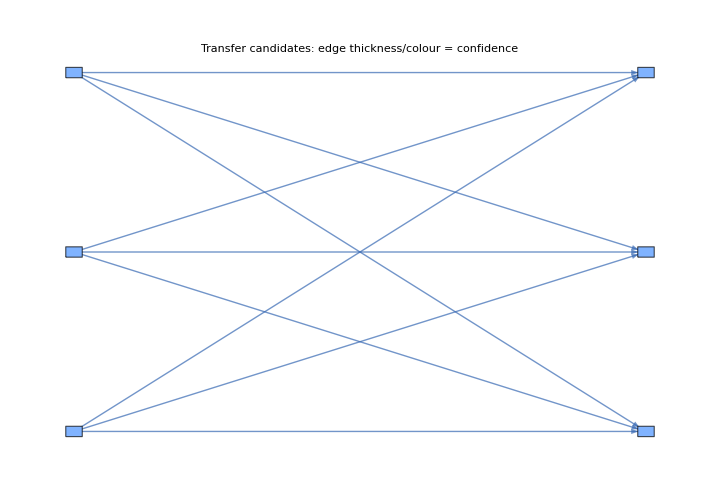

```mathematica
(* ::Package:: *)

(* ================================================================
   CELL 3 / 5 - VISUALISATION 6.1
   Tymoczko <-> Cutting transfer network. Self-contained: re-runs
   TransferCandidates so this cell works regardless of whether
   cell 2 truncated.
   ================================================================ *)

transferTC = TransferCandidates[TymoczkoCore, CuttingCore];

Print["6.1  Transfer network: Tymoczko (music) <-> Cutting (film)"];

Module[{tEdges, tStyles, allVerts, vstyles},
  tEdges = DirectedEdge[#["From"], #["To"]] & /@ transferTC;
  tStyles = MapThread[
    #1 -> Directive[
      Thickness[0.003 + 0.012 * #2],
      ColorData["TemperatureMap"][#2]
    ] &,
    {tEdges, #["Confidence"] & /@ transferTC}
  ];
  allVerts = Join[
    Keys[field[TymoczkoCore, "Mechanisms"]],
    Keys[field[CuttingCore, "Mechanisms"]]
  ];
  vstyles = Join[
    Map[# -> Lighter[Blue, 0.6] &,
        Keys[field[TymoczkoCore, "Mechanisms"]]],
    Map[# -> Lighter[Red, 0.6] &,
        Keys[field[CuttingCore, "Mechanisms"]]]
  ];
  Graph[
    allVerts,
    tEdges,
    VertexLabels -> Placed["Name", Tooltip],
    EdgeStyle -> tStyles,
    VertexStyle -> vstyles,
    VertexShapeFunction -> "Rectangle",
    GraphLayout -> "BipartiteEmbedding",
    ImageSize -> 720,
    PlotLabel -> Style[
      "Transfer candidates: edge thickness/colour = confidence",
      14, Bold
    ]
  ]
]
```

6.2  Removal cascade: voice_leading_parsimony out of Tymoczko

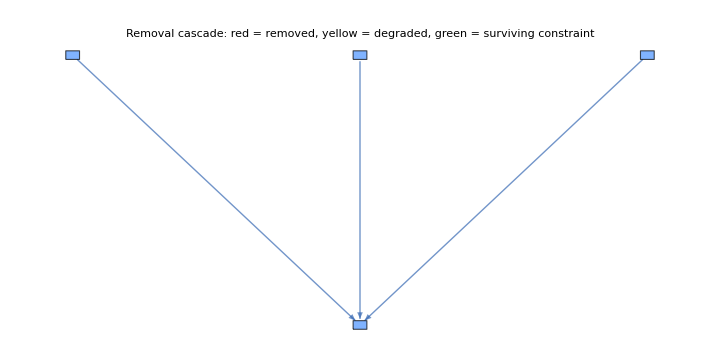

```mathematica
(* ::Package:: *)

(* ================================================================
   CELL 4 / 5 - VISUALISATION 6.2
   Tymoczko removal cascade. Self-contained.
   ================================================================ *)

deltaTymoczko = RemovalDelta[TymoczkoCore, "voice_leading_parsimony"];

Print["6.2  Removal cascade: voice_leading_parsimony out of Tymoczko"];

Module[{mIds, cIds, edges, vstyles},
  mIds = Keys[field[TymoczkoCore, "Mechanisms"]];
  cIds = Keys[field[TymoczkoCore, "Constraints"]];

  edges = Flatten @ Table[
    Module[{mech, deps},
      mech = field[TymoczkoCore, "Mechanisms"][m];
      deps = field[mech, "Compatibility"];
      If[!ListQ[deps], deps = {}];
      DirectedEdge[m, #] & /@ Intersection[deps, cIds]
    ],
    {m, mIds}
  ];

  vstyles = Join[
    {"voice_leading_parsimony" -> Directive[Red, EdgeForm[Black]]},
    Map[# -> Directive[Yellow, EdgeForm[Black]] &,
        deltaTymoczko["MechanismsDegraded"]],
    Map[# -> Directive[LightGreen, EdgeForm[Black]] &, cIds]
  ];

  Graph[
    Join[mIds, cIds],
    edges,
    VertexLabels -> Placed["Name", Tooltip],
    VertexStyle -> vstyles,
    VertexShapeFunction -> "Rectangle",
    ImageSize -> 720,
    PlotLabel -> Style[
      "Removal cascade: red = removed, yellow = degraded, " <>
      "green = surviving constraint",
      14, Bold
    ]
  ]
]
```

6.3  Methodology self-transfer graph: procedural isomorphism

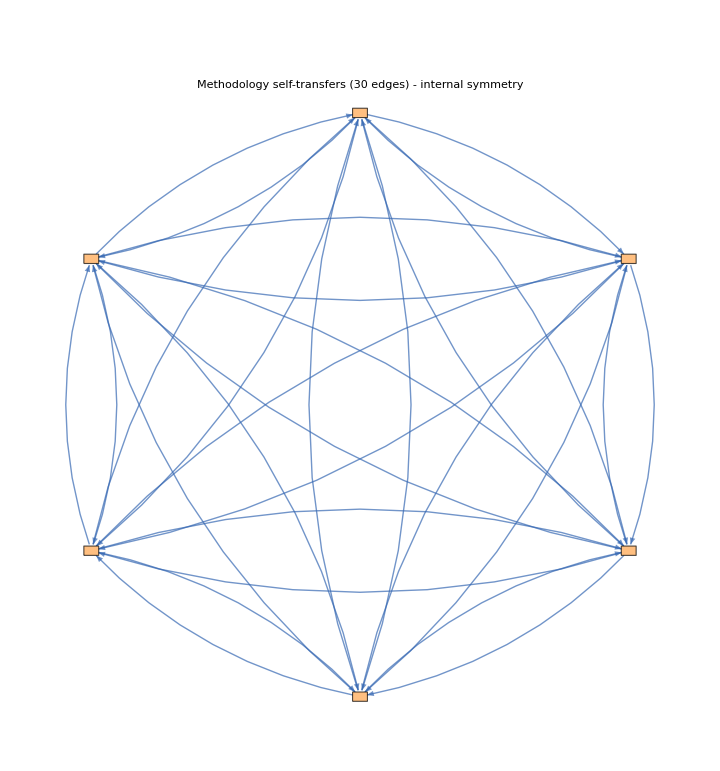

```mathematica
(* ::Package:: *)

(* ================================================================
   CELL 5 / 5 - VISUALISATION 6.3
   Methodology self-transfer graph. Self-contained.
   ================================================================ *)

recursiveResult = RecursiveAnalysis[MethodologyCore];

Print["6.3  Methodology self-transfer graph: procedural isomorphism"];

Module[{stEdges, stStyles, methodMechs},
  methodMechs = Keys[field[MethodologyCore, "Mechanisms"]];
  stEdges = DirectedEdge[#["From"], #["To"]] & /@
    recursiveResult["SelfTransfers"];
  stStyles = MapThread[
    #1 -> Directive[
      Thickness[0.002 + 0.008 * #2],
      ColorData["TemperatureMap"][#2]
    ] &,
    {stEdges, #["Confidence"] & /@ recursiveResult["SelfTransfers"]}
  ];

  Graph[
    methodMechs,
    stEdges,
    VertexLabels -> Placed["Name", Tooltip],
    EdgeStyle -> stStyles,
    VertexStyle -> Lighter[Orange, 0.5],
    VertexShapeFunction -> "Rectangle",
    GraphLayout -> "CircularEmbedding",
    ImageSize -> 720,
    PlotLabel -> Style[
      "Methodology self-transfers (" <>
      ToString[Length[stEdges]] <>
      " edges) - internal symmetry",
      14, Bold
    ]
  ]
]
```

6.4  Discrimination panel: where does comma-shape equivalence fire?

pair                                      candidates   max conf   min conf

Tymoczko (music)   <->  Cutting (film)        9          0.92       0.62

Tymoczko (music)   <->  NKS (computation)     11         0.68       0.30

Cutting (film)     <->  NKS (computation)     8         0.68       0.30

A. Tymoczko <-> Cutting (centerpiece)

Both commas have IrreducibilityKind = BoundaryDiscriminationAtLimit.

comma_shape_match fires on every pair; max confidence 0.92.

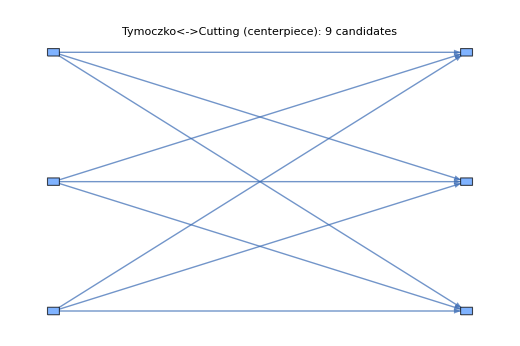

B. Tymoczko <-> NKS

IrreducibilityKinds differ (Boundary... vs BehaviouralPredicate...).

comma_shape_match never fires; max confidence drops to 0.68.

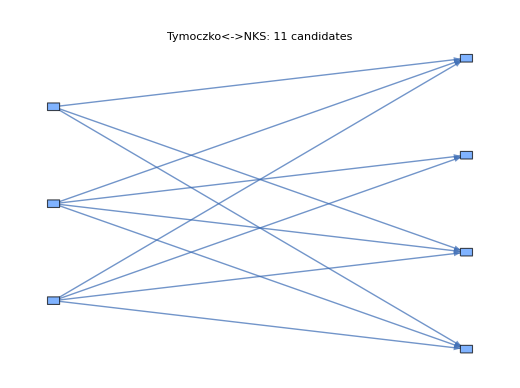

C. Cutting <-> NKS

IrreducibilityKinds also differ.

comma_shape_match never fires; max confidence drops to 0.68.

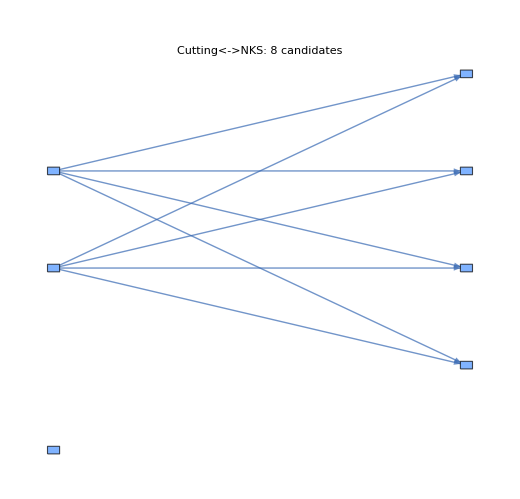

================================================================

What this panel shows

================================================================

The centerpiece pair (A) is the only one in which mechanism

edges reach 0.92 confidence. The other two pairs (B, C) cap at

0.68 - the next confidence tier, where shared mechanism Type

plus cross-domain fire but comma_shape_match does not.

The discriminating predicate is comma_shape_match. Tymoczko's

CommaPythagorean and Cutting's CommaShotBoundary share the

IrreducibilityKind 'BoundaryDiscriminationAtLimit', which is

the framework's articulated cross-domain claim from Paper 1

sec. 4.3. NKS's CommaRice has IrreducibilityKind

'BehaviouralPredicateUndecidability' - a different abstract

structural shape, which the algebra correctly identifies as

NOT comma-shape-equivalent to the other two.

Honest reading: the panel demonstrates that the algebra

discriminates on comma-shape, and that the high-confidence

centerpiece result is specific to the framework's claim, not

a uniform output. It does not establish the cross-domain

homology empirically; that remains the framework's open

question. It does establish that the framework's claim is

machine-checkable and that its computational signature is

the centerpiece's heat, not the panel's edge counts.

```mathematica
(* ::Package:: *)

(* ================================================================
   CELL 6 / 6 - VISUALISATION 6.4
   Discrimination panel. Compares Tymoczko<->Cutting (centerpiece)
   to Tymoczko<->NKS and Cutting<->NKS, to show that the algebra's
   high-confidence verdict is specific to the comma-equal pair.
   Self-contained: re-runs the three TransferCandidates queries.
   ================================================================ *)

transferTC = TransferCandidates[TymoczkoCore, CuttingCore];
transferTN = TransferCandidates[TymoczkoCore, NKSCore];
transferCN = TransferCandidates[CuttingCore, NKSCore];

maxConf[ts_] := If[Length[ts] == 0, 0, Max[#["Confidence"] & /@ ts]];
minConf[ts_] := If[Length[ts] == 0, 0, Min[#["Confidence"] & /@ ts]];

Print["6.4  Discrimination panel: where does comma-shape equivalence fire?"];
Print[""];
Print["  pair                                      candidates   max conf   min conf"];
Print["  Tymoczko (music)   <->  Cutting (film)        ",
      Length[transferTC], "          ",
      NumberForm[maxConf[transferTC], {3, 2}], "       ",
      NumberForm[minConf[transferTC], {3, 2}]];
Print["  Tymoczko (music)   <->  NKS (computation)     ",
      Length[transferTN], "         ",
      NumberForm[maxConf[transferTN], {3, 2}], "       ",
      NumberForm[minConf[transferTN], {3, 2}]];
Print["  Cutting (film)     <->  NKS (computation)     ",
      Length[transferCN], "         ",
      NumberForm[maxConf[transferCN], {3, 2}], "       ",
      NumberForm[minConf[transferCN], {3, 2}]];
Print[""];

renderPanel[transfers_, leftCore_, rightCore_, label_] :=
  Module[{tEdges, tStyles, allVerts, vstyles},
    tEdges = DirectedEdge[#["From"], #["To"]] & /@ transfers;
    tStyles = MapThread[
      #1 -> Directive[
        Thickness[0.003 + 0.012 * #2],
        ColorData["TemperatureMap"][#2]
      ] &,
      {tEdges, #["Confidence"] & /@ transfers}
    ];
    allVerts = Join[
      Keys[field[leftCore, "Mechanisms"]],
      Keys[field[rightCore, "Mechanisms"]]
    ];
    vstyles = Join[
      Map[# -> Lighter[Blue, 0.6] &,
          Keys[field[leftCore, "Mechanisms"]]],
      Map[# -> Lighter[Red, 0.6] &,
          Keys[field[rightCore, "Mechanisms"]]]
    ];
    Graph[
      allVerts,
      tEdges,
      VertexLabels -> Placed["Name", Tooltip],
      EdgeStyle -> tStyles,
      VertexStyle -> vstyles,
      VertexShapeFunction -> "Rectangle",
      GraphLayout -> "BipartiteEmbedding",
      ImageSize -> 520,
      PlotLabel -> Style[label, 12, Bold]
    ]
  ];

Print["A. Tymoczko <-> Cutting (centerpiece)"];
Print["   Both commas have IrreducibilityKind = BoundaryDiscriminationAtLimit."];
Print["   comma_shape_match fires on every pair; max confidence 0.92."];
Print @ renderPanel[transferTC, TymoczkoCore, CuttingCore,
  "Tymoczko<->Cutting (centerpiece): " <>
  ToString[Length[transferTC]] <> " candidates"];
Print[""];

Print["B. Tymoczko <-> NKS"];
Print["   IrreducibilityKinds differ (Boundary... vs BehaviouralPredicate...)."];
Print["   comma_shape_match never fires; max confidence drops to 0.68."];
Print @ renderPanel[transferTN, TymoczkoCore, NKSCore,
  "Tymoczko<->NKS: " <>
  ToString[Length[transferTN]] <> " candidates"];
Print[""];

Print["C. Cutting <-> NKS"];
Print["   IrreducibilityKinds also differ."];
Print["   comma_shape_match never fires; max confidence drops to 0.68."];
Print @ renderPanel[transferCN, CuttingCore, NKSCore,
  "Cutting<->NKS: " <>
  ToString[Length[transferCN]] <> " candidates"];
Print[""];

Print["================================================================"];
Print["What this panel shows"];
Print["================================================================"];
Print[""];
Print["The centerpiece pair (A) is the only one in which mechanism"];
Print["edges reach 0.92 confidence. The other two pairs (B, C) cap at"];
Print["0.68 - the next confidence tier, where shared mechanism Type"];
Print["plus cross-domain fire but comma_shape_match does not."];
Print[""];
Print["The discriminating predicate is comma_shape_match. Tymoczko's"];
Print["CommaPythagorean and Cutting's CommaShotBoundary share the"];
Print["IrreducibilityKind 'BoundaryDiscriminationAtLimit', which is"];
Print["the framework's articulated cross-domain claim from Paper 1"];
Print["sec. 4.3. NKS's CommaRice has IrreducibilityKind"];
Print["'BehaviouralPredicateUndecidability' - a different abstract"];
Print["structural shape, which the algebra correctly identifies as"];
Print["NOT comma-shape-equivalent to the other two."];
Print[""];
Print["Honest reading: the panel demonstrates that the algebra"];
Print["discriminates on comma-shape, and that the high-confidence"];
Print["centerpiece result is specific to the framework's claim, not"];
Print["a uniform output. It does not establish the cross-domain"];
Print["homology empirically; that remains the framework's open"];
Print["question. It does establish that the framework's claim is"];
Print["machine-checkable and that its computational signature is"];
Print["the centerpiece's heat, not the panel's edge counts."];
```